## Hubbard Model in Complex Plane

Contributors: Hugh G. A. Burton
Last Updated: 13-Nov-2020

We develop the Hubbard dimer as a consistent example for the convergence behaviour of MP theories.

1) Singlet FCI on real axis and complex plane
2) RMP expansion
3) UMP expansion

## Initialisation

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}"}];
```

```mathematica
(* Core Hamiltonian *)
Hc=({{-δϵ, -t}, {-t, δϵ}});
(* Two-electron integrals *)
G=Table[If[(μ==ν&&μ==λ&&μ==σ),U,0],{μ,2},{ν,2},{λ,2},{σ,2}];
c[θ_]={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
P[θ_,w_,x_]:=Table[c[θ]⟦i,w⟧c[θ]⟦j,x⟧,{i,2},{j,2}]
(* Core Hamiltonian and Fock matrices in MO basis *)
Fmo[θ1_,θ2_]= Transpose[c[θ1]].(Hc+Table[∑_(λ=1)^2 ∑_(σ=1)^2 ((P[θ1,1,1]⟦λ,σ⟧+P[θ2,1,1]⟦λ,σ⟧)G⟦μ,ν,λ,σ⟧-P[θ1,1,1]⟦λ,σ⟧G⟦μ,σ,λ,ν⟧),{μ,2},{ν,2}]).c[θ1];
Hmo[θ_]= Transpose[c[θ]].Hc.c[θ];
(* HF energy *)
Ehf[θα_,θβ_]:=1/2(Hmo[θα]⟦1,1⟧+Hmo[θβ]⟦1,1⟧+Fmo[θα,θβ]⟦1,1⟧+Fmo[θβ,θα]⟦1,1⟧)

(*Equations to evaluate matrix elements *)
SlaterCondon[θα_,θβ_,iOcc_,jOcc_]:=Module[{iα,jα,iβ,jβ},
{iα,iβ}=iOcc;
{jα,jβ}=jOcc;
If[(iα==jα&&iβ==jβ),∑_(μ=1)^2 ∑_(ν=1)^2 Hc⟦μ,ν⟧(P[θα,iα,jα]⟦ν,μ⟧+P[θβ,iβ,jβ]⟦ν,μ⟧)+1/2∑_(μ=1)^2 ∑_(ν=1)^2 ∑_(σ=1)^2 ∑_(τ=1)^2 ((P[θα,iα,jα]⟦ν,μ⟧+P[θβ,iβ,jβ]⟦ν,μ⟧)(P[θα,iα,jα]⟦σ,τ⟧+P[θβ,iβ,jβ]⟦σ,τ⟧)-(P[θα,iα,jα]⟦τ,μ⟧P[θα,iα,jα]⟦ν,σ⟧+P[θβ,iβ,jβ]⟦τ,μ⟧P[θβ,iβ,jβ]⟦ν,σ⟧))G⟦μ,ν,σ,τ⟧,
If[(iα≠jα&&iβ==jβ),∑_(μ=1)^2 ∑_(ν=1)^2 Hc⟦μ,ν⟧P[θα,iα,jα]⟦ν,μ⟧+∑_(μ=1)^2 ∑_(ν=1)^2 ∑_(σ=1)^2 ∑_(τ=1)^2 P[θα,iα,jα]⟦ν,μ⟧P[θβ,iβ,jβ]⟦σ,τ⟧G⟦μ,ν,σ,τ⟧,
If[(iα== jα&&iβ≠jβ),∑_(μ=1)^2 ∑_(ν=1)^2 Hc⟦μ,ν⟧P[θβ,iβ,jβ]⟦ν,μ⟧+∑_(μ=1)^2 ∑_(ν=1)^2 ∑_(σ=1)^2 ∑_(τ=1)^2 P[θα,iα,jα]⟦ν,μ⟧P[θβ,iβ,jβ]⟦σ,τ⟧G⟦μ,ν,σ,τ⟧,
If[(iα≠jα&&iβ≠jβ),∑_(μ=1)^2 ∑_(ν=1)^2 ∑_(σ=1)^2 ∑_(τ=1)^2 P[θα,iα,jα]⟦ν,μ⟧P[θβ,iβ,jβ]⟦σ,τ⟧G⟦μ,ν,σ,τ⟧,
0]
]]]
]
(* Occupation numbers for Hilbert space *)
Occ={{1,1},{1,2},{2,1},{2,2}};
Subscript[H, FCI][θα_,θβ_]=Table[SlaterCondon[θα,θβ,Occ⟦i⟧,Occ⟦j⟧],{i,1,4},{j,1,4}]//FullSimplify;
Subscript[H, sFCI][θα_,θβ_]=({{1, 0, 0, 0}, {0, 1/(√2), 1/(√2), 0}, {0, 0, 0, 1}}).Subscript[H, FCI][θα,θβ].({{1, 0, 0}, {0, 1/(√2), 0}, {0, 1/(√2), 0}, {0, 0, 1}})//FullSimplify;

(* MP reference Hamiltonian *)
H0[θα_,θβ_]=DiagonalMatrix[Table[Fmo[θα,θβ]⟦Occ⟦i⟧⟦1⟧,Occ⟦i⟧⟦1⟧⟧+Fmo[θβ,θα]⟦Occ⟦i⟧⟦2⟧,Occ⟦i⟧⟦2⟧⟧,{i,1,4}]]//FullSimplify;
Hmp[θα_,θβ_]=H0[θα,θβ]+λ(Subscript[H, FCI][θα,θβ]-H0[θα,θβ])//FullSimplify;
```

## Complex FCI

First construct symmetric dimer FCI Hamiltonian in the conventional RHF-based (θ = π/4) singlet CSFs.

```mathematica
Subscript[H, FCI][π/4,π/4]/.{δϵ->0}//MatrixForm
```

(-2 t+U/2 | 0 | U/2
0 | U | 0
U/2 | 0 | 2 t+U/2)

Here we see a block form, so we only get coupling between the ground-state and doubly-excited state. 
In this minimal basis, the open-shell singlet is given exactly by the corresponding CSF.

We can therefore apply the 2x2 Hamiltonian example to solve for the ground-state and doubly-excited state. 
This gives analytic energies as...

```mathematica
Eigenvalues[({{-2 t+U/2, 0, U/2}, {0, U, 0}, {U/2, 0, 2 t+U/2}})]
```

{U,1/2 (U-√(16 t^2+U^2)),1/2 (U+√(16 t^2+U^2))}

We can analytically find the exceptional point and find the corresponding energy (it’s pure imaginary!)

```mathematica
Solve[√(16 t^2+U^2)==0]
```

{{U→-4 ⅈ t},{U→4 ⅈ t}}

```mathematica
1/2 (U-√(16 t^2+U^2))/.{{U->-4 ⅈ t},{U->4 ⅈ t}}
```

{-2 ⅈ t,2 ⅈ t}

Plotting these energies as a function of U/t shows the avoided crossing on the real axis, 
and the exceptional point structure in the complex plane.

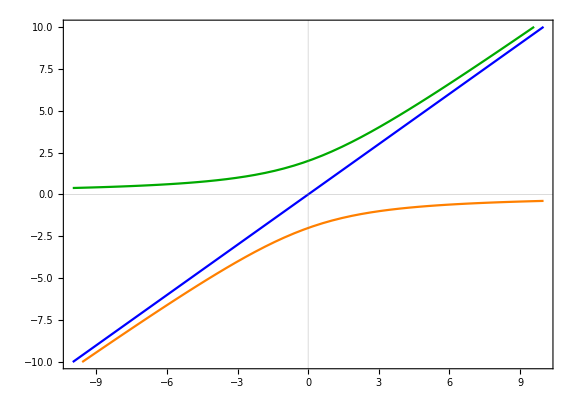

```mathematica
With[{t=1},Plot[{1/2 (U-√(16 t^2+U^2)),U,1/2 (U+√(16 t^2+U^2))},{U,-10,10},
PlotRange->{-10,10},PlotRangePadding->0,FrameStyle->Directive[Thick,18,Black],AspectRatio->0.7,
PlotStyle->{Orange,Blue,Darker[Green]},
FrameLabel->{MaTeX["U/t",Magnification->1.5],MaTeX["E_\\text{FCI}/t",Magnification->1.5]},
ImageSize->Large,PlotTheme->"Scientific"]]
```

```mathematica
With[{t=1},
Show[Plot3D[{Re[1/2 ((rU+ⅈ zU)-√(16 t^2+(rU+ⅈ zU)^2))],Re[(rU+ⅈ zU)],Re[1/2 ((rU+ⅈ zU)+√(16 t^2+(rU+ⅈ zU)^2))]},{rU,-10,10},{zU,0,10},
BoxRatios->{1, 1, 1},ImageSize->Large,PlotStyle->Opacity[0.7],Mesh->None,ViewPoint->{1.3,-1.6,0.7},
AxesLabel->{
MaTeX["\\text{Re}(U/t)",Magnification->1.5],
MaTeX["\\text{Im}(U/t)",Magnification->1.5],
Rotate[MaTeX["\\text{Re}(E_\\text{FCI})/t",Magnification->1.5],π/2]},
AxesStyle->Directive[Thick,18,Black]],
ListPointPlot3D[{{0,4,0}},PlotStyle->Black]]]
```

-Graphics3D-

## RHF and UHF

We will need to identify analytic forms for the  RHF and UHF solutions to use in the RMP and UMP expansions. 
We’ve done this to death before, so here it is in a relatively un-interesting form...

```mathematica
Ehf[θα,θβ]/.{δϵ->0}//FullSimplify
```

1/2 (U+U Cos[2 θα] Cos[2 θβ]-2 t (Sin[2 θα]+Sin[2 θβ]))

Minimize[1/2 (U+U Cos[2 θα] Cos[2 θβ]-2 t (Sin[2 θα]+Sin[2 θβ])),{θα,θβ}]

```mathematica
Solve[{D[1/2 (U+U Cos[2 θα] Cos[2 θβ]-2 t (Sin[2 θα]+Sin[2 θβ])),θα]==0,D[1/2 (U+U Cos[2 θα] Cos[2 θβ]-2 t (Sin[2 θα]+Sin[2 θβ])),θβ]==0},{θα,θβ}]/.{ C[1]->0, C[2]->0}
```

{{θα→-π/4,θβ→-π/4},{θα→-π/4,θβ→π/4},{θα→π/4,θβ→-π/4},{θα→π/4,θβ→π/4},{θα→1/2 ArcTan[-(√(-4 t^2+U^2))/U,-(2 t)/U],θβ→1/2 ArcTan[-(√(-4 t^2+U^2))/U,-(2 t)/U]},{θα→1/2 ArcTan[-(√(-4 t^2+U^2))/U,(2 t)/U],θβ→1/2 ArcTan[(√(-4 t^2+U^2))/U,(2 t)/U]},{θα→1/2 ArcTan[(√(-4 t^2+U^2))/U,-(2 t)/U],θβ→1/2 ArcTan[(√(-4 t^2+U^2))/U,-(2 t)/U]},{θα→1/2 ArcTan[(√(-4 t^2+U^2))/U,(2 t)/U],θβ→1/2 ArcTan[-(√(-4 t^2+U^2))/U,(2 t)/U]}}

```mathematica
{RHF1,UHF1,UHF2,RHF2}={{θα->-π/4,θβ->-π/4},{θα->-π/4,θβ->π/4},{θα->π/4,θβ->-π/4},{θα->π/4,θβ->π/4}};
{sbRHF1,sbUHF1,sbRHF2,sbUHF2}={{θα->1/2 ArcTan[-(√(-4 t^2+U^2))/U,-(2 t)/U],θβ->1/2 ArcTan[-(√(-4 t^2+U^2))/U,-(2 t)/U]},{θα->1/2 ArcTan[-(√(-4 t^2+U^2))/U,(2 t)/U],θβ->1/2 ArcTan[(√(-4 t^2+U^2))/U,(2 t)/U]},{θα->1/2 ArcTan[(√(-4 t^2+U^2))/U,-(2 t)/U],θβ->1/2 ArcTan[(√(-4 t^2+U^2))/U,-(2 t)/U]},{θα->1/2 ArcTan[(√(-4 t^2+U^2))/U,(2 t)/U],θβ->1/2 ArcTan[-(√(-4 t^2+U^2))/U,(2 t)/U]}};
```

```mathematica
1/2 (U+U Cos[2 θα] Cos[2 θβ]-2 t (Sin[2 θα]+Sin[2 θβ]))/.{RHF1,UHF1,UHF2,RHF2,sbRHF1,sbUHF1,sbUHF2,sbRHF2}//FullSimplify
```

{1/2 (4 t+U),U/2,U/2,1/2 (-4 t+U),(2 t^2)/U+U,-(2 t^2)/U,-(2 t^2)/U,(2 t^2)/U+U}

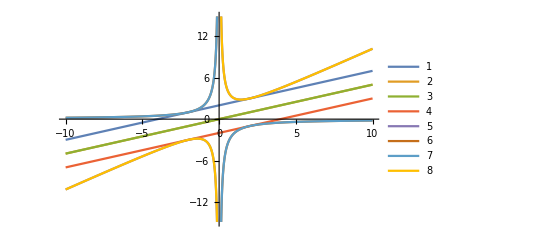

```mathematica
With[{t=1},Plot[{1/2 (4 t+U),U/2,U/2,1/2 (-4 t+U),(2 t^2)/U+U,-(2 t^2)/U,-(2 t^2)/U,(2 t^2)/U+U},{U,-10,10},PlotLegends->Automatic]]
```

## RMP

We can now consider the RMP series convergence. To do this, we get the Fock operator in RMP as our reference and

```mathematica
Subscript[H, RMP]=Hmp[π/4,π/4]/.{δϵ->0}//FullSimplify//MatrixForm
```

(-2 t+U-(U λ)/2 | 0 | 0 | (U λ)/2
0 | U-(U λ)/2 | (U λ)/2 | 0
0 | (U λ)/2 | U-(U λ)/2 | 0
(U λ)/2 | 0 | 0 | 2 t+U-(U λ)/2)

```mathematica
Eigenvalues[({{-2 t+U-(U λ)/2, 0, 0, (U λ)/2}, {0, U-(U λ)/2, (U λ)/2, 0}, {0, (U λ)/2, U-(U λ)/2, 0}, {(U λ)/2, 0, 0, 2 t+U-(U λ)/2}})]
```

{U,U-U λ,1/2 (2 U-U λ-√(16 t^2+U^2 λ^2)),1/2 (2 U-U λ+√(16 t^2+U^2 λ^2))}

First, we identify that the radius of convergence is defined by the exceptional points at λ = ± 4t / U. 
We illustrate this by plotting the energy expansions at orders of λ just below and above the radius of convergence

```mathematica
SeriesCoefficient[1/2 (2 U-U λ-√(16 t^2+U^2 λ^2))/.{U->3},{λ,0,0}]
```

3-2 √(t^2)

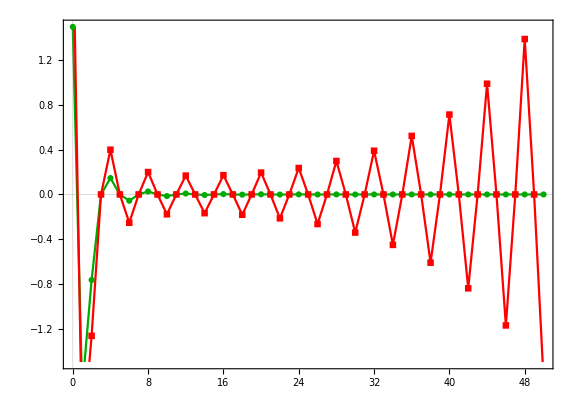

```mathematica
With[{t=1},ListPlot[
{Table[{i,SeriesCoefficient[1/2 (2 U-U λ-√(16 t^2+U^2 λ^2))/.{U->3.5},{λ,0,i}]},{i,0,50}],
Table[{i,SeriesCoefficient[1/2 (2 U-U λ-√(16 t^2+U^2 λ^2))/.{U->4.5},{λ,0,i}]},{i,0,50}]},
PlotStyle->{Darker[Green],Red},PlotRange->{-1.5,1.5},PlotTheme->"Scientific",PlotRangePadding->0,Joined->True,PlotMarkers->Automatic,
AspectRatio->0.7,FrameStyle->Directive[Thick,18,Black],
FrameLabel->{MaTeX["n",Magnification->1.5],MaTeX["E^{(n)}_\\text{RMP}/t",Magnification->1.5]},
ImageSize->Large,
PlotLegends->Placed[{MaTeX["U = 3.5 t",Magnification->1.5],MaTeX["U = 4.5 t",Magnification->1.5]},{0.2,0.85}]
]]
```

We can also plot the corresponding Riemann surface that connects the reference and exact values at the same two U/t ratios

```mathematica
With[{t=1,U=3.5},
Show[Plot3D[{Re[1/2 (2 U-U (rλ+ⅈ zλ)-√(16 t^2+U^2 (rλ+ⅈ zλ)^2))],Re[ U-U (rλ+ⅈ zλ)],Re[1/2 (2 U-U (rλ+ⅈ zλ)+√(16 t^2+U^2 (rλ+ⅈ zλ)^2))]},{rλ,-1.5,1.5},{zλ,0,2},
BoxRatios->{1, 1, 1},ImageSize->Large,PlotStyle->Opacity[0.7],Mesh->None,ViewPoint->{1.3,-1.6,0.7},PlotRange-> {-5,10},
AxesLabel->{
MaTeX["\\text{Re}(\\lambda)",Magnification->1.5],
MaTeX["\\text{Im}(\\lambda)",Magnification->1.5],
Rotate[MaTeX["\\text{Re}(E_\\text{FCI})/t",Magnification->1.5],π/2]},
AxesStyle->Directive[Thick,18,Black]],
ListPointPlot3D[{{0,4t/U, U }},PlotStyle->Black]]]
```

-Graphics3D-

```mathematica
With[{t=1,U=4.5},
Show[Plot3D[{Re[1/2 (2 U-U (rλ+ⅈ zλ)-√(16 t^2+U^2 (rλ+ⅈ zλ)^2))],Re[ U-U (rλ+ⅈ zλ)],Re[1/2 (2 U-U (rλ+ⅈ zλ)+√(16 t^2+U^2 (rλ+ⅈ zλ)^2))]},{rλ,-1.5,1.5},{zλ,0,2},
BoxRatios->{1, 1, 1},ImageSize->Large,PlotStyle->Opacity[0.7],Mesh->None,ViewPoint->{1.3,-1.6,0.7},PlotRange-> {-5,12},
AxesLabel->{
MaTeX["\\text{Re}(\\lambda)",Magnification->1.5],
MaTeX["\\text{Im}(\\lambda)",Magnification->1.5],
Rotate[MaTeX["\\text{Re}(E_\\text{FCI})/t",Magnification->1.5],π/2]},
AxesStyle->Directive[Thick,18,Black]],
ListPointPlot3D[{{0,4t/U, U }},PlotStyle->Black]]]
```

-Graphics3D-

### An interesting connection...

Let’s take a quick look at the exceptional points we have found so far...

FCI:             1   = ± i 4t / U
RMP:          λ_c= ± i 4t / U

So we see that the magnitudes of each exceptional point are all the same... 
Is it possible that each of these exceptional point is dictated by the fundamental exceptional point in the FCI energy?
Or is this an artefact of our incredible simple model?

## UMP

We can now consider the MP expansion from the symmetry-broken UHF reference state.
The optimal rotation angles are computed in the HF section and are given as...

```mathematica
sbUHF1
```

{θα→1/2 ArcTan[-(√(-4 t^2+U^2))/U,(2 t)/U],θβ→1/2 ArcTan[(√(-4 t^2+U^2))/U,(2 t)/U]}

We use these to construct the UMP Hamiltonian problem ...

```mathematica
Hump[U_,t_,λ_]=Hmp[1/2 ArcTan[-(√(-4 t^2 +U^2))/U,(2 t)/U],1/2 ArcTan[(√(-4 t^2+U^2))/U,(2 t)/U]]/.{δϵ->0}//FullSimplify;
Hump[U,t,λ]//MatrixForm
```

(-(2 t^2 λ)/U | 0 | 0 | (2 t^2 λ)/U
0 | U-(2 t^2 λ)/U | (2 t^2 λ)/U | (2 t √(-4 t^2+U^2) λ)/U
0 | (2 t^2 λ)/U | U-(2 t^2 λ)/U | -(2 t √(-4 t^2+U^2) λ)/U
(2 t^2 λ)/U | (2 t √(-4 t^2+U^2) λ)/U | -(2 t √(-4 t^2+U^2) λ)/U | -2 U (-1+λ)+(6 t^2 λ)/U)

As expected, the spatial and spin contamination makes the exact eigenvalues more difficult to work with and introduces many more
coupling elements into the expression.

```mathematica
Eigenvalues[({{-(2 t^2 λ)/U, 0, 0, (2 t^2 λ)/U}, {0, U-(2 t^2 λ)/U, (2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U}, {0, (2 t^2 λ)/U, U-(2 t^2 λ)/U, -(2 t √(-4 t^2+U^2) λ)/U}, {(2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U, -(2 t √(-4 t^2+U^2) λ)/U, -2 U (-1+λ)+(6 t^2 λ)/U}})]//FullSimplify
```

Mathematica doesn’t want to give a closed form for these energies, but we can extract the singlet states from the “root” function...

```mathematica
Eigenvalues[Hump[U,t,λ]]
```

{U,Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,1]/U,Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,2]/U,Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,3]/U}

```mathematica
Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,1]/U//ToRadicals//FullSimplify
```

1/(3 U)(3 U^2-2 U^2 λ+(-12 t^2 U^2 (-2+λ) λ+U^4 (3-6 λ+4 λ^2))/((U^6 λ (-9+2 (9-4 λ) λ)+18 t^2 U^4 λ (3+2 (-2+λ) λ)+1/2 √(4 U^8 λ^2 (U^2 (-9+2 (9-4 λ) λ)+18 t^2 (3+2 (-2+λ) λ))^2-4 (-12 t^2 U^2 (-2+λ) λ+U^4 (3-6 λ+4 λ^2))^3))^(1/3))+(U^6 λ (-9+2 (9-4 λ) λ)+18 t^2 U^4 λ (3+2 (-2+λ) λ)+1/2 √(4 U^8 λ^2 (U^2 (-9+2 (9-4 λ) λ)+18 t^2 (3+2 (-2+λ) λ))^2-4 (-12 t^2 U^2 (-2+λ) λ+U^4 (3-6 λ+4 λ^2))^3))^(1/3))

```mathematica
ϵSinglet[U_,t_,λ_]={
Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,1]/U,
Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,2]/U,
Root[4 t^2 U^4 λ-4 t^2 U^4 λ^2+(2 U^4-8 t^2 U^2 λ-2 U^4 λ+4 t^2 U^2 λ^2) #1+(-3 U^2+2 U^2 λ) #1^2+#1^3&,3]/U};
```

With no closed form, we rely on graphical representations to inspect the radius of convergence. 
Here we use a cylinder to plot the radius of convergence, and inspect the situation for different U/t values.

### U = 7t

Here we are well towards the strong correlation regime, where it is known that UMP will be slowly convergent but RMP diverges.
We see a single exceptional point on the ground-state surface which falls just outside (maybe on?) the radius of convergence. 
An exceptional point this close to the radius of convergence gives an increasingly slow convergence of the UMP series, but it will converge eventually!

Note that the ground-state energy is remarkably flat since the UHF energy is a pretty good estimate. 
Most of the UMP expansion is actually correcting the spin-contamination in the wave function.

On the other hand, there is an exceptional point on the excited energy surface that is well within the radius of convergence.
We can therefore say that the use of a symmetry-broken UHF wave function can retain a convergent ground-state perturbation series
at the expense of a divergent excited-state perturbation series. (Note: the orbitals are not optimised for excited-state here).
In contrast, the RMP expansion was always convergent for the open-shell excited state (which was a single CSF) while
the radius of convergence for the doubly-excited state was identical to the ground-state as this was the only exceptional point.

```mathematica
Show[
{Plot3D[Evaluate[Re[ϵSinglet[7,1,rλ+ⅈ zλ]]],{rλ,-0.2,1.2},{zλ,0,1},PlotStyle->Opacity[0.7],BoxRatios->{1, 1, 1},ImageSize->Large,MaxRecursion->6],
Graphics3D[{Opacity[0.5],Cylinder[{{0,0,-4},{0,0,20}},1]}]},PlotRange->{{0,1.2},{0,1.2},{-2.1,17}},Boxed->False
]
```

-Graphics3D-

### U = 3t

If we now consider a case within the radius of convergence for RMP, we see that the ground-state exceptional point has moved
slightly further beyond the radius of convergence. However, this is still much closer than the RMP exceptional point, so the convergence
is now slower than the RMP convergence.

On the other hand, the excited-state exceptional point is still within the radius of convergence and its expansion will therefore diverge.

```mathematica
Show[
{Plot3D[Evaluate[Re[ϵSinglet[3,1,rλ+ⅈ zλ]]],{rλ,-0.2,1.2},{zλ,0,5},PlotStyle->Opacity[0.7],BoxRatios->{1, 1, 1},ImageSize->Large,MaxRecursion->6],
Graphics3D[{Opacity[0.5],Cylinder[{{0,0,-4},{0,0,20}},1]}]},PlotRange->{{0,1.2},{0,1.2},{-2,6.}},Boxed->False
]
```

-Graphics3D-

### Will the UMP ground-state always converge?

This important question can be paraphrased as “does the ground-state EP ever fall within the radius of convergence?”. 
To answer this, we can consider the fixed FCI point on the corresponding Riemann surface

Firstly the nature of the symmetry-breaking in UHF will always give an energy that is an increasingly accurate estimate of the exact energy. 
This is because UHF can capture the strong correlation effects by spatially separating the two electrons.
At the fixed point λ=1, the energies of the states will always be the FCI energy, and this is independent of the reference orbitals.

If the ground-state is a good FCI estimate, it will cross from λ=0 to 1 in a “flat” fashion. This makes it far less likely to interact with 
a higher energy state, so it is less likely to encounter an exceptional point. Equally, the first excited state will tend towards the 
exact first-excited singlet FCI energy. It is possible for these states to cross on the real-λ line, but any crossing must occur
beyond λ=1 because otherwise they would not connect to the correct fixed point.

So what happens to the RMP exceptional point?

In the RMP case, the convergence is controlled by an exceptional point between the ground- and doubly-excited RHF configurations.
These two states interact strongly in the λ expansion in the large U/t limit because the ground RHF state is heavily 
contaminated by the 3rd FCI singlet  state. It is this strong interaction that causes the exceptional point, and ultimately
the divergence. 

In the UMP case, this “energetic” contamination from the 3rd FCI state is reduced (removed?) by replacing it with triplet contamination.
The strong interaction is then shifted from the ground configuration to the “open-shell” configurations in the UHF framework, 
since the 3rd FCI singlet state contributions are rotated into the virtual orbitals.
This explains why we see the severe excited-state exceptional point in the UMP Riemann surface.
In a way, we can think of this as the “open-shell” configurations “shielding” the ground-state from the strong interaction (and
exceptional point), hence we have more robust convergence in ground-state, but less robust convergence in excited-state.

### Summary

In this notebook, we have investigated the convergence of the RMP and UMP series in the Hubbard dimer through visualisation 
on Riemann surfaces. 

Our main conclusions:
1) Exact FCI problem has intrinsic exceptional points in the U/t complex plane, corresponding to an avoided crossing on the real axis.
2) When RMP converges, it does so fast. Both the ground- and excited-states have the same radius of convergence as they are controlled
     by the same exceptional point. However, this exceptional point is prone to moving within the radius of convergence, causing divergence.
3) Allowing the orbitals to break symmetry in UMP gives a more robust convergence for ground-state by removing energetic contamination
     in the reference at the expense of adding triplet contamination. This convergence is at the expense of a massively divergent excited-state
     perturbation series.
     
Moving Forwards...
One of the more significant ideas could be the effect of orbital optimisation on the radius of convergence. In the UHF case we saw that 
ground-state orbital optimisation massively improved the robustness of the ground-state MP expansion. Would excited-state
orbital optimisation would do the same for excited-state MP expansions at the expense of ground-state convergence? 
If so, this would provide reassurance in the computation of dynamic correlation for state-specific excited states, and would suggest
that we should expect reliable behaviour in orbital-optimised coupled-cluster expansions.